```mathematica
L=100;

AM = ConstantArray[0,{L,2,L,2}];
Do[
(* the potential *)
AM[[l+0,1,l+0,1]] = +u/2;
AM[[l+0,2,l+0,2]] = -u/2;

(* on-site hopping *)
AM[[l+0,2,l+0,1]] = +v;
If[l<L,
AM[[l+1,1,l+0,2]] = +w;
];
,{l,1,L}]
Η=ArrayReshape[AM,{2L,2L}];
Η+=Η†;
```

```mathematica
Ω=π;
spec={};
vecs={};
Do[
{eval,evec}=Eigensystem[Η/.{u->Sin[Ω t],v->1+Cos[Ω t], w->1}];
order = Ordering[eval];
eval=eval[[order]];
evec=evec[[order]];
AppendTo[spec,eval];
AppendTo[vecs,evec];
,{t,0,2,.05}]
```

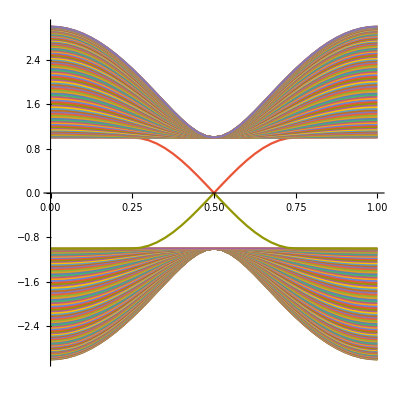

```mathematica
ListPlot[specᵀ,Joined->True,AspectRatio->1,DataRange->{0,1}]
```

```mathematica
Manipulate[ListPlot[{(Abs[vecs[[ii,L]]]^2)[[;;;;2]]+(Abs[vecs[[ii,L]]]^2)[[2;;;;2]],(Abs[vecs[[ii,L+1]]]^2)[[;;;;2]]+(Abs[vecs[[ii,L+1]]]^2)[[2;;;;2]]},PlotStyle->Black,PlotRange->Full,Joined->True],{ii,1,Length[vecs],1}]
```

```mathematica
f[x_]=Piecewise[{8x,x<1/8},{1,1/8≤ x<3/8 },{1-8()}]
```

```mathematica
Ω=π;
spec={};
vecs={};
Do[
{eval,evec}=Eigensystem[Η/.{u->Sin[Ω t],v->1+Cos[Ω t], w->1}];
order = Ordering[eval];
eval=eval[[order]];
evec=evec[[order]];
AppendTo[spec,eval];
AppendTo[vecs,evec];
,{t,0,2,.05}]
```

```mathematica
ListPlot[specᵀ,Joined->True,AspectRatio->1,DataRange->{0,1}]
```